# Решаване на уравнения и системи от уравнения

Уравнение в системата Mathematica, можем да запишем по следния начин (обърнете внимание на двойното равенство, не бива да се бърка с оператора за присвояване “=”):

x^2+2x-7 == 0

За решаване на алгебрични уравнения и системи от алгебреични уравнения, се използва функцията Solve:

```mathematica
Solve[x^2+2x-7 == 0,x]
```

{{x→-1-2 √2},{x→-1+2 √2}}

```mathematica
Solve[x^2+2x-7 = 0,x](*Ако поставим просто знак за равенство, ще получим съобщение за грешка - не можем да присвоим стойност на лявата страна на уравнението*)
```

Set::write: Tag Plus in -7+2 x+x^2 is Protected.

Solve::naqs: 0 is not a quantified system of equations and inequalities.

Solve[0,x]

Solve връща като резултат списък с прваила за заместване (replacement rules). Такъв тип изрази можем да използваме, за да заместим символа x в даден израз, със съответната стойност, намираща се след стрелката:

```mathematica
solution=Solve[x^2+2x-7 == 0,x]
ReplaceAll[x^2+2x-7 ,solution[[1]]]//Simplify
x^2+2x-7 /.solution[[1]]//Simplify
```

{{x→-1-2 √2},{x→-1+2 √2}}

0

0

Solve търси решението в аналитичен вид, т.е във вид на алгебричен израз. Ясно е, обаче, че това невинаги е възможно. Известно е, че за намиране на корените на уравнения от пета и по-висока степен, не съществува обща формула (Теорема на Абел-Руфини).
Ако се налага да решаваме такъв тип уравнения, можем да използваме NSolve, който връща числена апроксимация на корените на у-то:

```mathematica
Solve[5 x^5+12 x^3-5x+8==0,x]
```

{{x→Root[8-5 #1+12 #1^3+5 #1^5&,1]},{x→Root[8-5 #1+12 #1^3+5 #1^5&,2]},{x→Root[8-5 #1+12 #1^3+5 #1^5&,3]},{x→Root[8-5 #1+12 #1^3+5 #1^5&,4]},{x→Root[8-5 #1+12 #1^3+5 #1^5&,5]}}

```mathematica
NSolve[5 x^5+12 x^3-5x+8==0,x]
```

{{x→-0.919084},{x→-0.0883087-1.67731 ⅈ},{x→-0.0883087+1.67731 ⅈ},{x→0.547851-0.562967 ⅈ},{x→0.547851+0.562967 ⅈ}}

```mathematica
NSolve[5 x^5+12 x^3-5x+8==0,x,Reals](*Можем да подадем опция на (N)Solve с която да специфицираме областта, в която да се търси решението*)
```

{{x→-0.919084}}

Ако разлгедаме, обаче, едно общо линейно уравенение a x + b = 0, където a и b са параметри, Solve няма да ни даде съвсем изчерпателно решение. В такъв случай, можем да използваме Reduce. Reduce дава всички възможни решения на дадено уравнение/система от уравнения, в зависимост от стойностите на участващите параметри, докато Solve връща само общо решение. Обърнете внимание, че Reduce, за разлика от Solve, връща логически израз като резултат. Това го прави и подходящ за решаване на неравенства.

```mathematica
Solve[а x+b==0,x]
```

{{x→-b/а}}

```mathematica
Reduce[а x+b==0,x]
```

(b==0&&а==0)||(а≠0&&x==-b/а)

```mathematica
Solve[3x-2≤0,x,Reals]
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}

```mathematica
Reduce[3x -2<=0,x]
```

x≤2/3

За трансцендентни уравнения, например cos(x) = x,  2^x= x^2 и  т.н., в общия случай не съществува аналитично решение, и това налага необходимостта от численото им решаване. NSolve е функция, която дава числена апроксимация на решенията на алгебрични уравнения. Намирането на корени на произволни уравнения може да бъде далеч по-сложна задача. FindRoot е функция за числено намиране на корени на произволни уравнения. Тя използва итерационни методи,  като започва търсенето на корен от дадено начално приближение.

```mathematica
{Solve[Cos[x]==x,x],Reduce[Cos[x]==x,x],NSolve[Cos[x]==x,x]}
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

{Solve[Cos[x]==x,x],Reduce[Cos[x]==x,x],NSolve[Cos[x]==x,x]}

```mathematica
FindRoot[Cos[x]==x,{x,0}]
```

{x→0.739085}

```mathematica
FindRoot[Cos[x]==x,{x,1000}](*Добър резултат при произволно начално приближение*)
```

{x→0.739085}

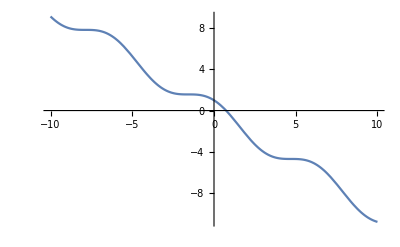

```mathematica
Plot[Cos[x]==x,{x,-10,10}]
```

```mathematica
FindRoot[Cos[x]==x,{x,0},WorkingPrecision->30](*С помощта на опцията WorkingPrecision задаваме броя на значещите цифри в резултата*)
```

{x→0.739085133215160641655312087674}

По подразбиране FindRoot използва метода на Нютон, т.е използва стойността на производната на функцията при пресмятане на приближението (вж. допълнителните задачи към упр.3 и 4). Ако в стойността на производната около корена има особености, това може да доведе до проблеми с пресмятанията - например коренът може да бъде “прескочен”.

```mathematica
FindRoot[x^(1/3)==0,{x,0.00001}]
```

{x→-4.31158×10^-16+4.43548×10^-29 ⅈ}

```mathematica
x^(1/3)/.FindRoot[x^(1/3)==0,{x,0.000001}](*След заместване в уравненнието, не получаваме 0. *)
```

6.46632×10^-6-1.56997×10^-19 ⅈ

```mathematica
{D[x^(1/3),x],Limit[D[x^(1/3),x],x->0]}
```

{1/(3 x^(2/3)),∞}

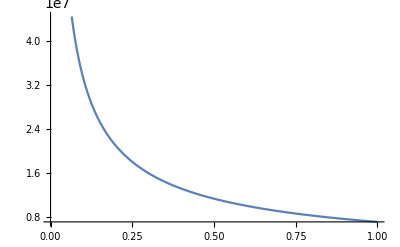

```mathematica
Plot[D[x^(1/3),x]/.x->xx,{xx,0,0.00000000001}]
```

Ако началното приближение е далеч от стойността на действителния корен, силно вероятно е алгоритъмът да приключи работа при достигане на локален минимум на функцията. При численото решаване на уравнения, изключително важен е изборът на добро начално приближение! При избора на такова, може да ни бъде полезно изследването на графиката на функцията.

```mathematica
sol0=FindRoot[Log[x]-2Cos[x]==0,{x,20}] (*FindRoot връща грешка, лесно се проверява, че получената стойност 18.823 не е корен на у-то.*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→18.823}

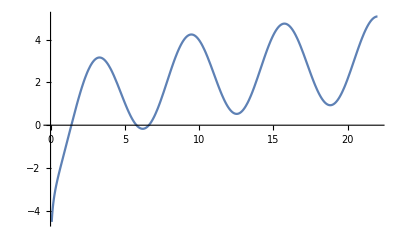

```mathematica
Plot[Log[x]-2Cos[x],{x,0,22}]
```

```mathematica
sol0=FindRoot[Log[x]-2Cos[x]==0,{x,{1,5,7}}]
```

{x→{1.40129,5.78292,6.61695}}

## Системи линейни уравнения

### Системи от две уравнения с две неизвестни

За решаване на линейни системи от уравнения в системата Mаthematica има два основни подхода. Единият е да използваме функциите Solve/NSolve, като изброим уравненията от системата в явен вид. Другият е да запишем системата във векторно-матрична форма и да използваме функцията LinearSolve.

a1 x + b1 y = c1
a2 x + b2 y = c2

```mathematica
Solve[{a1 x + b1 y ==0, a2 x + b2 y ==2},{x,y}]
```

{{x→(2 b1)/(a2 b1-a1 b2),y→(2 a1)/(-a2 b1+a1 b2)}}

```mathematica
LinearSolve[{{a1,b1},{a2,b2}},{c1,c2}]
```

{(b2 c1-b1 c2)/(-a2 b1+a1 b2),(a2 c1-a1 c2)/(a2 b1-a1 b2)}

Да разгледаме следните системи:

А) 	2x + y = 0		B)  2x + y = 0                C)  2x + y = 3
	3x - y = 2  		     4x + 2y = 2		     4x + 2y = 6

```mathematica
LinearSolve[{{2,1},{3,-1}},{0,2}]
```

{2/5,-4/5}

```mathematica
LinearSolve[{{2,1},{4,2}},{0,2}]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{2,1},{4,2}},{0,2}]

```mathematica
LinearSolve[{{2,1},{4,2}},{3,6}](*В случай на безброй много решения, LinerSolve връща едно частно такова.*)
```

{3/2,0}

```mathematica
Solve[{2x+y==3,4x+2y==6},{x,y}](*Solve ни дава връзка между неизвестните. Всяка двойка, удовлятворяваща тези условия, е решение на системата.*)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→3-2 x}}

Редовете на тази линейна система задават уравнения на две прави. Ако системата има единствено решение, то ще представлява координатите на пресечната точка на тези две прави (А). В случай, че редовете/стълбовете на матрицата са лин. зависими, то правите, които уравненията от системата описват, са успоредни - нямат пресечна точка и систамата няма решение. При определени условия за дясната част обаче, двете прави може да съвпадат една с друга - тогава системата има безброй много решения.

Нека сега разгледаме стълбовете на системите.  Можем да запишем, например, системата А) в следния вид:

x (2
3) + y (   1
-1) = (0
2)

По същество, неизвестните x и y представляват коефициенти в някаква линейна комбинация на стълбовете на матрицата. За да има системата решение, векторът на десните части трябва да може да бъде представен като линейна комбинация на стълбовете на матрицата. Казано с други думи, векторът на десните части трябва да лежи в пространството, определено от стълбовете на матрицата. За системата А) имаме два лин. независими стълба, които определят цялото пространство R2. Следователно, за произволна дясна част, системата ще има решение, тъй като всеки един вектор от пространството R2 може да бъде зададен чрез линейна комбинация на на два линейнo независими вектора от същото пространство. За системата B) имаме линейно зависими редове/стълбове. Правите, зададени от редовете на системата са успордени една на друга, а вектор-стълбовете лежат върху права линия. Система B) няма решение, тъй като векторът на десните части не лежи върху тази права. Ако дясната част лежи върху правата, то правите, определени от редовете на системата съвпадат, и системата има безброй много решения, какъвто е случаят със система C).

Всяка от изброените възможности, можете да видите на графиката по-долу.

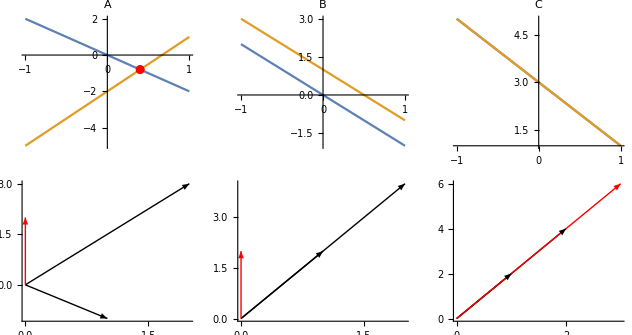

```mathematica
GraphicsGrid[{{Show[Plot[{-2x,3x-2},{x,-1,1},PlotLabel->"A"],
ListPlot[{{2/5,-4/5}},PlotMarkers->Automatic,PlotStyle->Red]
],
Plot[{-2x,(2-4x)/2},{x,-1,1},PlotLabel->"B"],
Plot[{3-2x,(6-4x)/2},{x,-1,1},PlotLabel->"C"]
},
{Graphics[{Arrowheads->0.1,Arrow[{{0,0},{2,3}}],Arrow[{{0,0},{1,-1}}],Thick,Red,Arrow[{{0,0},{0,2}}]},Axes->True],
Graphics[{Arrowheads->0.1,Arrow[{{0,0},{2,4}}],Arrow[{{0,0},{1,2}}],Thick,Red,Arrow[{{0,0},{0,2}}]},Axes->True],
Graphics[{Arrowheads->0.1,Arrow[{{0,0},{2,4}}],Arrow[{{0,0},{1,2}}],Thick,Red,Arrow[{{0,0},{3,6}}]},Axes->True]
}
}]
```

### 3D system

За системи 3x3, горните заключения могат да се обобщят в тримерното пространство. Система А) има единствено решение, система B) има безброй много решения, а система C) няма решение. Геометричната интерпретация на редовете и стълбовете на всяка от системите, можете да видите на графиката по-долу.

    A)	 3 x + 2 y  -   z = 1, 		B)   3 x + 2 y   - z = 1,		C)  3 x + 2 y   -  z = 1,
	 2 x - 2  y + 4z = - 2,		     12 x + 8 y - 4z = 4,		    12 x + 8 y - 4 z = 20,
	  - x + 8 y  -   z = 0.		        - x + 8 y   - z = 0.		       - x + 8 y   -  z = 0.

```mathematica
LinearSolve[{{3,2,-1},{2,-2,4},{-1,8,-1}},{1,-2,0}]
```

{1/6,-1/18,-11/18}

```mathematica
Solve[{3 x+2 y-z,12 x+8 y-4 z,-x+8 y-z}=={1,4,0}](*Безброй много решения от този вид*)
```

{{y→-1/6+(2 x)/3,z→-4/3+(13 x)/3}}

```mathematica
LinearSolve[{{3,2,-1},{12,8,-4},{-1,8,-1}},{1,20,0}]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{3,2,-1},{12,8,-4},{-1,8,-1}},{1,20,0}]

```mathematica
GraphicsGrid[{{Show[
ContourPlot3D[{3x+2y-z==1,2x-2y+4z==-2,-x+8y-z==0},{x,-10,10},{y,-10,10},{z,-10,10},PlotRange->All,PlotLabel->"A"],
ListPointPlot3D[{sol},PlotStyle->{Red,PointSize[0.05]}]
],
Show[
ContourPlot3D[{3x+2y-z==1,12x+8y-4z==4,-x+8y-z==0},{x,-10,10},{y,-10,10},{z,-10,10},PlotRange->All,PlotLabel->"B"]],
Show[
ContourPlot3D[{3x+2y-z==1,12x+8y-4z==20,-x+8y-z==0},{x,-10,10},{y,-10,10},{z,-10,10},PlotRange->All,PlotLabel->"C"]]
},
{Graphics3D[{Arrow[{{0,0,0},{3,2,-1}}],Arrow[{{0,0,0},{2,-2,4}}],Arrow[{{0,0,0},{-1,4,-1}}],Red,Arrow[{{0,0,0},{1,-2,0}}]},Axes->True,BoxRatios->{1, 1, 1}],
Graphics3D[{Arrow[{{0,0,0},{3,12,-1}}],Arrow[{{0,0,0},{2,8,8}}],Arrow[{{0,0,0},{-1,-4,-1}}],Red,Arrow[{{0,0,0},{1,4,0}}]},Axes->True,BoxRatios->{1, 1, 1}],
Graphics3D[{Arrow[{{0,0,0},{3,12,-1}}],Arrow[{{0,0,0},{2,8,8}}],Arrow[{{0,0,0},{-1,-4,-1}}],Red,Arrow[{{0,0,0},{1,20,0}}]},Axes->True,BoxRatios->{1, 1, 1}]
}}]
```

-Graphics-

#### Хомогенни системи

Да разгелдаме една хомогенна система. LinearSolve ще ни върне нулев вектор.
x + 2y + 3z = 0
4x + 5y +6z = 0
7x +8y + 9z = 0.

```mathematica
m1={{1,2,3},{4,5,6},{7,8,9}};
LinearSolve[m1,{0,0,0}]
```

{0,0,0}

Лесно можем да проверим, обаче, че системата има нетривиално решение. За да го получим, можем да използваме Solve, който ще ни даде алгебрични изрази, задаващи връзка между неизвестните. Другата опция е да използваме функцията NullSpace, която връща базис на ядрото на матрицата на системата. Тогава всяка линейна комбинация на резултатните вектори от NullSpace ще бъде решение на системата (всяка точка от червената права на графиката долу).

```mathematica
{Det[m1],MatrixRank[m1]}
Solve[m1.{x,y,z}=={0,0,0},{x,y,z}]
NullSpace[{{1,2,3},{4,5,6},{7,8,9}}]
```

{0,2}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→-2 x,z→x}}

{{1,-2,1}}

```mathematica
Show[
Plot3D[{(-x-2y)/3,(-4x-5y)/6,(-7x-8y)/9},{x,-10,10},{y,-10,10},PlotRange->All],
Graphics3D[{Thick,Red,Arrow[{-10*{1,-2,1},10*{1,-2,1}}]}]
]
```

-Graphics3D-